This program calculates the velocity profile of a Newtonian fluid with horizontal laminar flow. It does so for three different geometries: rectangular, cylindrical and spherical. In the momentum balance, the term for gravity is ignored since this program only models horizontal flow. Bulk flow terms are also cancelled by assuming that the momentum due to bulk flow stays constant.

The program takes into account a few possible scenarios to consider different boundary conditions. One scenario is that the fluid is surrounded by stationary walls/plates, in which case the shear stress is 0 at the center and a symmetrical velocity profile. Another scenario is that there is a gas liquid interface, where shear stress is 0 as well. If neither of these scenarios apply, the last scenario that’s covered is that the velocity of the fluid is known at 2 points.

## Key

parSol = particular solution
genSol = general solution
rhsVdiffeq = right hand side of the differential equation for velocity
velProf = velocity profile
specificVelProf = specific velocity profile given inputted conditions for the fluid

```mathematica
SetOptions[EvaluationNotebook[],Background->White]
```

# Stationary Walls or Gas-Liquid Interface

## Rectangular Geometry (Flow Between Slabs)

{{τ[x]→(-d1 Pl+d1 Po+Pl x-Po x)/L}}

Shear stress: τ(x) = (5-x)/2

print[(-2 d1 d2 Pl+d2^2 Pl+2 d1 d2 Po-d2^2 Po+2 d1 Pl x-2 d1 Po x-Pl x^2+Po x^2+2 L V1 μ)/(2 L μ)]

Velocity profile: V(x) = 1/8 (16-10 x+x^2)

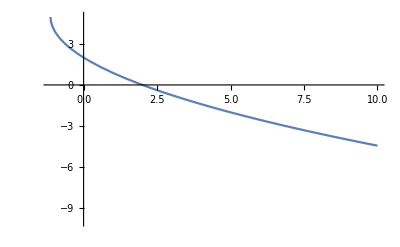

```mathematica
ClearAll["Global`*"]

(*τ'[x]=.*)
(*d1input=Input["x-value where τ=0: "];
V1input=Input["Known velocity: "];
d2input=Input["x-value of known velocity: "];
Linput=Input["Length of plates: "];
μinput=Input["Fluid viscosity: "];
Poinput=Input["Inlet pressure: "];
Plinput=Input["Outlet pressure: "];
*)
d1input=5;
V1input=0;
d2input=2;
Linput=2;
μinput=2;
Poinput=3;
Plinput=2;

parSolTau=DSolve[{τ'[x]==(Pl-Po)/L,τ[d1]==0},τ[x],x];
Print[parSolTau]
Print["Shear stress: τ(x) = ",τ[x]/.parSolTau[[1]]/.{d1->d1input,Po->Poinput,Pl->Plinput, L->Linput}]

rhsVdiffeq = ((τ[x]/.parSolTau)/(-μ))[[1]];
parSolV = DSolve[{V'[x]==rhsVdiffeq, V[d2]==V1},V[x],x];
velProf=(V[x]/.parSolV)[[1]];
print[velProf]

specificVelProf=velProf/.{d1->d1input,V1->V1input,d2->d2input,L->Linput, μ->μinput, Po->Poinput,Pl->Plinput};
Print["Velocity profile: V(x) = ", specificVelProf]

flip=Solve[y==specificVelProf,x];
F1[y_]=x/.flip;
If[d1input==0,
Plot[F1[y],{y,-10,10},PlotRange->{-10,10}]
]
If[d1input>0,
Plot[F1[y],{y,-10,10},PlotRange->{-10,d1input}]
]
If[d1input<0,
Plot[F1[y],{y,-10,10},PlotRange->{d1input,10}]
]
(*cylindrical*)

(*spherical*)
```

## Two Known Velocities